```mathematica
k22x21x11:=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000, kappa = 1\\kappa = 0\\k2,2 k2,1 k1,1.dat"][[All, {1,2,3,4,5}]]
k33x32x11:=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000, kappa = 1\\kappa = 0\\k3,3 k3,2 k1,1.dat"][[All, {1,2,3,4,5}]]
k55x54x11:=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000, kappa = 1\\kappa = 0\\k5,5 k5,4 k1,1.dat"][[All, {1,2,3,4,5}]]
k22x21x11a:=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000, kappa = 1\\kappa = 0\\k2,2 k2,1 k1,1 - all games.dat"][[All, {1,2,3,4,5}]]
k33x32x11a:=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000, kappa = 1\\kappa = 0\\k3,3 k3,2 k1,1 - all games.dat"][[All, {1,2,3,4,5}]]
k55x54x11a:=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000, kappa = 1\\kappa = 0\\k5,5 k5,4 k1,1 - all games.dat"][[All, {1,2,3,4,5}]]
```

```mathematica
stabline:=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\stabilityline l0-001.dat"]
fitstab1[x_]:=-1.0257106915360754+4.407107406679403 x^0.5+30.247317445231058 x
```

```mathematica
instab[v_]:= Select[v, #[[2]] > fitstab1[#[[1]]] & ]
instabDiff[w_] := ReplacePart[#,3->#[[3]]-#[[5]] ]&/@w
chaosregion[x_]:=Select[x, #[[2]] <-0.5 &&#[[1]] < 0.003&]
```

```mathematica
k2pos :=instabDiff[k22x21x11a]
k3pos := instabDiff[k33x32x11a]
k5pos :=  instabDiff[k55x54x11a]
```

```mathematica
k22diffs:=k2pos[[All,3]] 
k33diffs :=k3pos[[All, 3]]
k55diffs := k5pos[[All, 3]]
```

```mathematica
density[v_]:=PDF[SmoothKernelDistribution[v,MaxRecursion->Automatic, PerformanceGoal->"Quality"], x]
```

```mathematica
Mean[k22diffs]
Skewness[k22diffs]
Mean[k33diffs]
Skewness[k33diffs]
Mean[k55diffs]
Skewness[k55diffs]
```

0.00639819

0.0980867

-0.0362626

0.1027

-0.0379834

-0.263608

```mathematica
k3311pdf =density[k33x32x11a[[All, 3]]]-density[k33x32x11a[[All, 5]]]
k2211pdf =density[k22x21x11a[[All, 3]]]-density[k22x21x11a[[All, 5]]]
k5511pdf =density[k55x54x11a[[All, 3]]]-density[k55x54x11a[[All, 5]]]
```

(Piecewise[{{InterpolatingFunction[{{-8.48503,5.51978}},<>][x], -8.48503≤x≤5.51978}, {0, True}}])-(Piecewise[{{InterpolatingFunction[{{-8.43372,5.37489}},<>][x], -8.43372≤x≤5.37489}, {0, True}}])

(Piecewise[{{InterpolatingFunction[{{-8.90852,5.80773}},<>][x], -8.90852≤x≤5.80773}, {0, True}}])-(Piecewise[{{InterpolatingFunction[{{-8.85085,5.66239}},<>][x], -8.85085≤x≤5.66239}, {0, True}}])

(Piecewise[{{InterpolatingFunction[{{-8.52199,5.07496}},<>][x], -8.52199≤x≤5.07496}, {0, True}}])-(Piecewise[{{InterpolatingFunction[{{-8.44765,5.74399}},<>][x], -8.44765≤x≤5.74399}, {0, True}}])

```mathematica
k3311cpdf =density[chaosregion[k33x32x11a][[All, 3]]]-density[chaosregion[k33x32x11a][[All, 5]]]
k2211cpdf =density[chaosregion[k22x21x11a][[All, 3]]]-density[chaosregion[k22x21x11a][[All, 5]]]
k5511cpdf =density[chaosregion[k55x54x11a][[All, 3]]]-density[chaosregion[k55x54x11a][[All, 5]]]
```

-(Piecewise[{{InterpolatingFunction[{{-3.98123,5.85168}},<>][x], -3.98123≤x≤5.85168}, {0, True}}])+(Piecewise[{{InterpolatingFunction[{{-3.93854,5.27714}},<>][x], -3.93854≤x≤5.27714}, {0, True}}])

-(Piecewise[{{InterpolatingFunction[{{-6.77263,6.19045}},<>][x], -6.77263≤x≤6.19045}, {0, True}}])+(Piecewise[{{InterpolatingFunction[{{-6.73903,6.046}},<>][x], -6.73903≤x≤6.046}, {0, True}}])

-(Piecewise[{{InterpolatingFunction[{{-3.76421,5.44847}},<>][x], -3.76421≤x≤5.44847}, {0, True}}])+(Piecewise[{{InterpolatingFunction[{{-3.61998,5.15402}},<>][x], -3.61998≤x≤5.15402}, {0, True}}])

```mathematica
SetOptions[Plot, BaseStyle->(FontSize->16)]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→FontSize→16,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

SetOptions::optnf: BaseStyle is not a known option for Show.

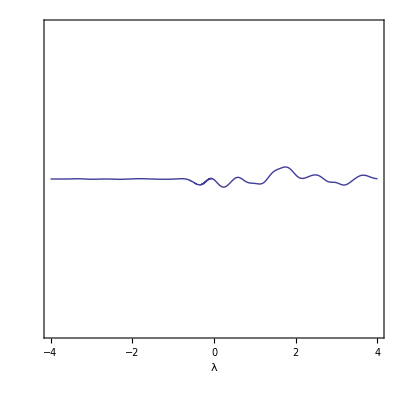

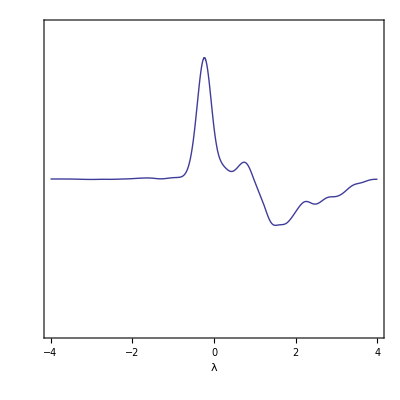

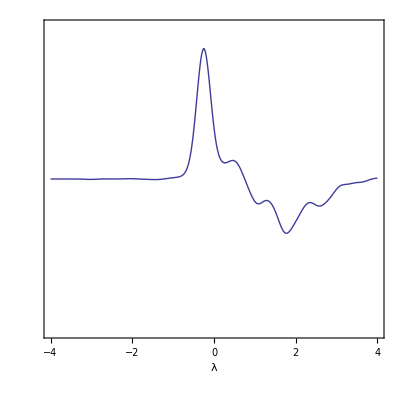

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\pdfk2211.pdf

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\pdfk3311.pdf

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\pdfk5511.pdf

```mathematica
pdfk2211=Plot[k2211cpdf, {x,-4,4}, PlotRange->{-0.15,0.15}, AxesOrigin->{0,0},  AspectRatio->1/1,Frame->True, FrameLabel->{{None,"Δpdf_(k (2, 2) - k (1, 1))"},{λ,None}},Filling->None,FrameTicks->{{None, All},{All,None}}]
pdfk3311=Plot[k3311cpdf, {x,-4,4}, PlotRange->{-0.15,0.15}, AxesOrigin->{0,0},  AspectRatio->1/1,Frame->True, FrameLabel->{{None,"Δpdf_(k (3, 3) - k (1, 1))"},{λ,None}}, Filling->None,FrameTicks->{{None, All},{All,None}}]
pdfk5511=Plot[k5511cpdf, {x,-4,4}, PlotRange->{-0.15,0.15}, AxesOrigin->{0,0},  AspectRatio->1/1,Frame->True, FrameLabel->{{None,"Δpdf_(k (5, 5) - k (1, 1))"},{λ,None}},Filling->None,FrameTicks->{{None, All},{All,None}}]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\pdfk2211.pdf",pdfk2211]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\pdfk3311.pdf",pdfk3311]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\pdfk5511.pdf",pdfk5511]
```

```mathematica
ListPlot[k3pos[[All, {3,5}]], PlotRange -> All]
```

```mathematica
SetOptions[DensityPlot, PlotRangePadding -> 0]
SetOptions[ListDensityPlot, PlotRangePadding->0]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&,#2&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→0,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,LabelStyle→{},LightingAngle→None,MaxPlotPoints→Automatic,Mesh→None,MeshFunctions→{#1&,#2&},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→0,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},VertexColors→Automatic}

```mathematica
colorf[x_]:= (x+ 1.8)/4.8
```

```mathematica
colorf3[x_]:= 100x
legend2 := DensityPlot[y,{x,0,0.1},{y,0,0.01}, ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][colorf3[#]]&), AspectRatio -> 10/1, Frame->True, FrameTicks ->  {{False, All}, {False, False}}, FrameLabel -> {{None,None},{None,α}}, BaseStyle->(FontSize->16),RotateLabel->False]
legend3:= DensityPlot[y,{x,0,0.1},{y,-2,3}, ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][colorf[#]]&), AspectRatio -> 10/1, Frame->True, FrameTicks ->  {{False, All}, {False, False}}, FrameLabel -> {{None, λ},{None,None}}, BaseStyle->(FontSize->16),RotateLabel->False]
range :={{-9,6},{-9,6},All}
```

```mathematica
colorf2[x_]:=x + 1
legend := DensityPlot[y,{x,0,0.1},{y,-1,0}, ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][colorf2[#]]&), AspectRatio -> 10/1, Frame->True, FrameTicks ->  {{False, All}, {False, False}}, FrameLabel -> {{None, Γ},{None,None}}, BaseStyle->(FontSize->16), RotateLabel->False]
```

```mathematica
SetOptions[Export, ImageResolution->350]
```

SetOptions::optnf: ImageResolution is not a known option for Export.

SetOptions[Export,ImageResolution→350]

```mathematica
k2211scatterg=Show[Graphics[{ColorData["Rainbow"][ #2 +1],PointSize[0.005],Point[{#3,#5}]}&@@@k22x21x11a,Axes->True],Plot[x, {x,-9,6},PlotStyle->{Black,Dashed}], Frame->True, BaseStyle->(FontSize->16),ImageSize->Large,FrameLabel->{{"λ_(k (2, 2))",legend},{"λ_(k (1, 1))", None}}, RotateLabel->False]
k2211scattera=Show[Graphics[{ColorData["Rainbow"][ 100#1],PointSize[0.005],Point[{#3,#5}]}&@@@k22x21x11a,Axes->True],Plot[x, {x,-9,6},PlotStyle->{Black,Dashed}], Frame->True, BaseStyle->(FontSize->16),ImageSize->Large,FrameLabel->{{"λ_(k (2, 2))",legend2},{"λ_(k (1, 1))", None}}, RotateLabel->False]
```

-Graphics-

-Graphics-

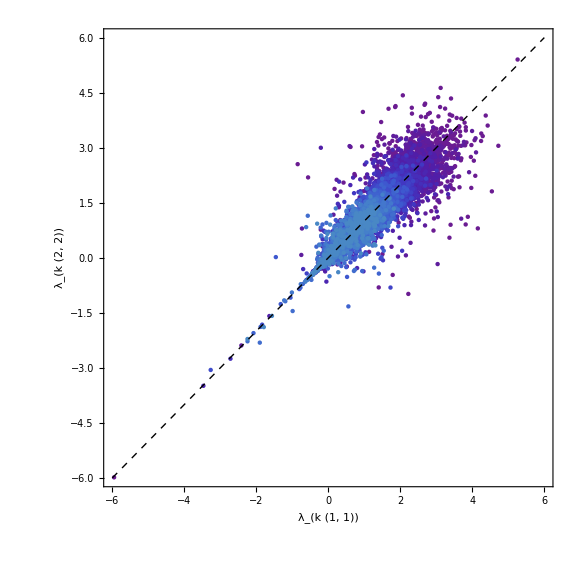

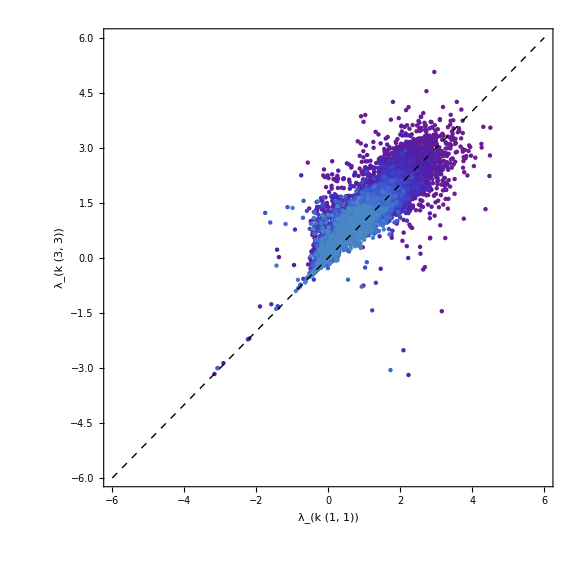

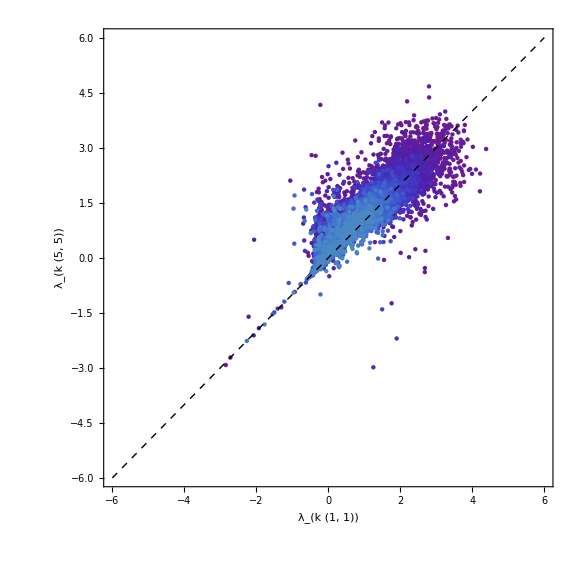

```mathematica
k2211scatterchaos=Show[Graphics[{ColorData["Rainbow"][ 100#1],PointSize[0.0055],Point[{#3,#5}]}&@@@chaosregion[k22x21x11a],Axes->True],Plot[x, {x,-6,6},PlotStyle->{Black,Dashed}], Frame->True, BaseStyle->(FontSize->18),ImageSize->Large,FrameLabel->{{"λ_(k (2, 2))",legend2},{"λ_(k (1, 1))", None}}, RotateLabel->False]
k3311scatterchaos=Show[Graphics[{ColorData["Rainbow"][ 100#1],PointSize[0.0055],Point[{#3,#5}]}&@@@chaosregion[k33x32x11a],Axes->True],Plot[x, {x,-6,6},PlotStyle->{Black,Dashed}], Frame->True, BaseStyle->(FontSize->18),ImageSize->Large,FrameLabel->{{"λ_(k (3, 3))",legend2},{"λ_(k (1, 1))", None}}, RotateLabel->False]
k5511scatterchaos=Show[Graphics[{ColorData["Rainbow"][ 100#1],PointSize[0.0055],Point[{#3,#5}]}&@@@chaosregion[k55x54x11a],Axes->True],Plot[x, {x,-6,6},PlotStyle->{Black,Dashed}], Frame->True, BaseStyle->(FontSize->18),ImageSize->Large,FrameLabel->{{"λ_(k (5, 5))",legend2},{"λ_(k (1, 1))", None}}, RotateLabel->False]
```

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\scatterk22x11g.png" ,k2211scatterg, ImageResolution->350]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\scatterk22x11a.png" ,k2211scattera, ImageResolution->350]
```

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\scatterk22x11chaos.png" ,k2211scatterchaos, ImageResolution->350]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\scatterk33x11chaos.png" ,k3311scatterchaos, ImageResolution->350]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\scatterk55x11chaos.png" ,k5511scatterchaos, ImageResolution->350]
```

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\scatterk22x11chaos.pdf" ,k2211scatterchaos]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\scatterk33x11chaos.pdf" ,k3311scatterchaos]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\scatterk55x11chaos.pdf" ,k5511scatterchaos]
```

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\scatterk22x11chaos.pdf

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\scatterk33x11chaos.pdf

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\scatterk55x11chaos.pdf

```mathematica
Show[Graphics[{ColorData["Rainbow"][ 100#1],Point[{#3,#5}]}&@@@chaosregion[k33x32x11a],Axes->True],Plot[x, {x,-9,6},PlotStyle->{Black,Dashed}], Frame->True,ImageSize->Large,FrameLabel->{{"λ_(k (3, 3))",legend2},{"λ_(k (1, 1))", None}}, RotateLabel->False]
Show[Graphics[{ColorData["Rainbow"][ 100#1],Point[{#3,#5}]}&@@@chaosregion[k55x54x11a],Axes->True],Plot[x, {x,-9,6},PlotStyle->{Black,Dashed}], Frame->True,ImageSize->Large,FrameLabel->{{"λ_(k (5, 5))",legend2},{"λ_(k (1, 1))", None}}, RotateLabel->False]
```

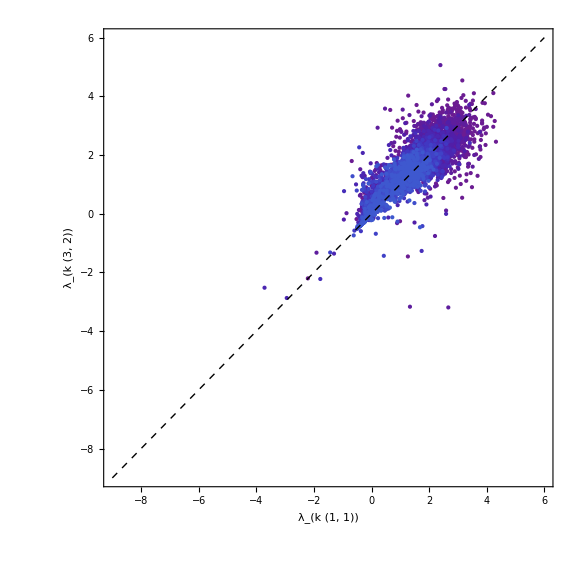

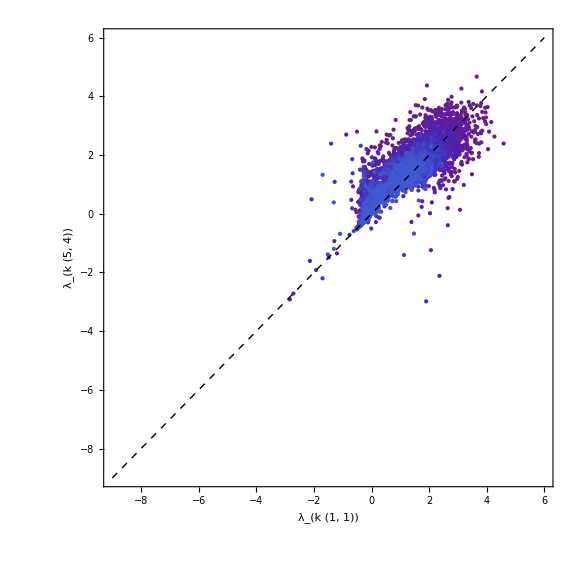

```mathematica
Show[Graphics[{ColorData["Rainbow"][ 100#1],Point[{#4,#5}]}&@@@chaosregion[k33x32x11a],Axes->True],Plot[x, {x,-9,6},PlotStyle->{Black,Dashed}], Frame->True,ImageSize->Large,FrameLabel->{{"λ_(k (3, 2))",legend2},{"λ_(k (1, 1))", None}}, RotateLabel->False]
Show[Graphics[{ColorData["Rainbow"][ 100#1],Point[{#4,#5}]}&@@@chaosregion[k55x54x11a],Axes->True],Plot[x, {x,-9,6},PlotStyle->{Black,Dashed}], Frame->True,ImageSize->Large,FrameLabel->{{"λ_(k (5, 4))",legend2},{"λ_(k (1, 1))", None}}, RotateLabel->False]
```

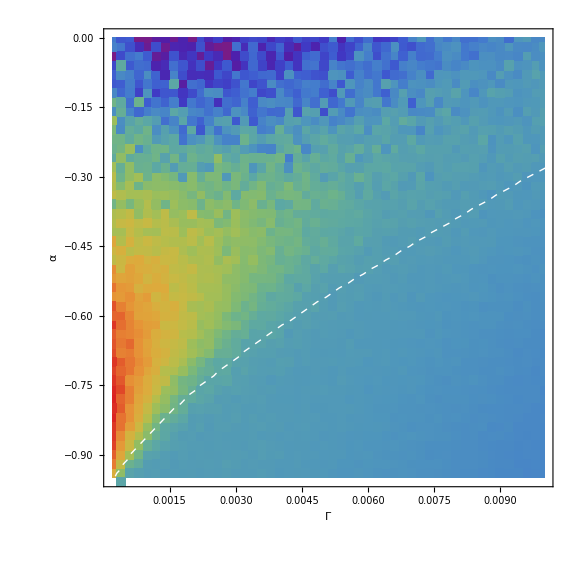

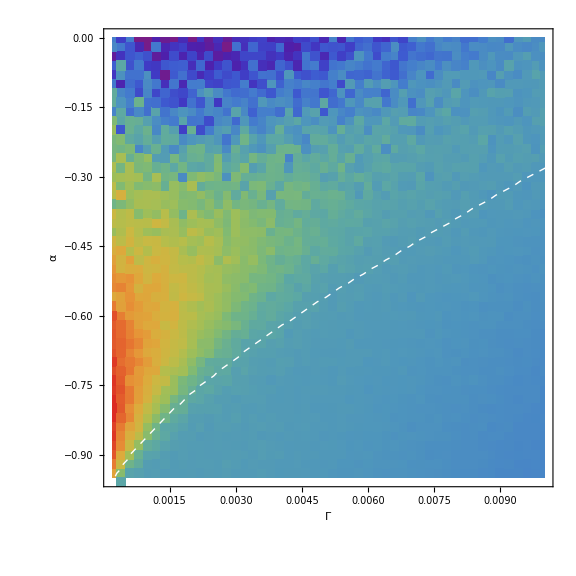

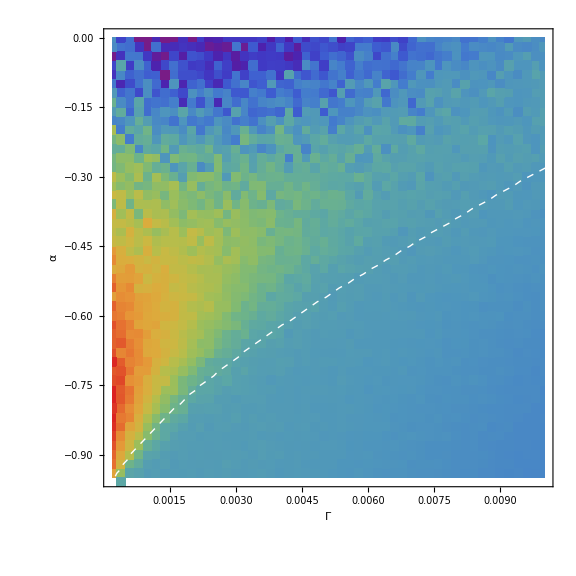

```mathematica
k11lyap=Show[ListDensityPlot[k22x21x11[[All,{1,2,5}]],PlotRange->{{0.0002,0.01} ,{-0.95,0},All},InterpolationOrder->0,ColorFunctionScaling ->False,ImageSize->Large,ColorFunction->(ColorData["Rainbow"][(colorf[#])]&)],ListLinePlot[stabline,PlotStyle->{White,Dashed}],Frame->True,FrameLabel->{{"α",legend3},{"Γ", None}}, RotateLabel->False,BaseStyle->{FontSize->16}]
k21lyap =Show[ListDensityPlot[k22x21x11[[All,{1,2,4}]],PlotRange->{{0.0002,0.01} ,{-0.95,0},All},InterpolationOrder->0,ColorFunctionScaling ->False,ImageSize->Large,ColorFunction->(ColorData["Rainbow"][(colorf[#])]&)],ListLinePlot[stabline,PlotStyle->{White,Dashed,Thin}],Frame->True,FrameLabel->{{"α",legend3},{"Γ", None}}, RotateLabel->False,BaseStyle->{FontSize->16}]
k22lyap =Show[ListDensityPlot[k22x21x11[[All,{1,2,3}]],PlotRange->{{0.0002,0.01} ,{-0.95,0},All},InterpolationOrder->0,ColorFunctionScaling ->False,ImageSize->Large,ColorFunction->(ColorData["Rainbow"][(colorf[#])]&)],ListLinePlot[stabline,PlotStyle->{White,Dashed,Thin}],Frame->True,FrameLabel->{{"α",legend3},{"Γ", None}}, RotateLabel->False,BaseStyle->{FontSize->16}]
```

```mathematica
k33lyap =Show[ListDensityPlot[k33x32x11[[All,{1,2,3}]],PlotRange->{{0.0002,0.01} ,{-0.95,0},All},InterpolationOrder->0,ColorFunctionScaling ->False,ImageSize->Large,ColorFunction->(ColorData["Rainbow"][(colorf[#])]&)],ListLinePlot[stabline,PlotStyle->{White,Dashed,Thin}],Frame->True,FrameLabel->{{"α",legend3},{"Γ", None}}, RotateLabel->False,BaseStyle->{FontSize->16}]
k55lyap=Show[ListDensityPlot[k55x54x11[[All,{1,2,3}]],PlotRange->{{0.0002,0.01} ,{-0.95,0},All},InterpolationOrder->0,ColorFunctionScaling ->False,ImageSize->Large,ColorFunction->(ColorData["Rainbow"][(colorf[#])]&)],ListLinePlot[stabline,PlotStyle->{White,Dashed,Thin}],Frame->True,FrameLabel->{{"α",legend3},{"Γ", None}},RotateLabel->False,BaseStyle->{FontSize->16}]
```

$Aborted

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\k11lyap2.pdf",k11lyap]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\k22lyap2.pdf",k22lyap]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\k21lyap2.pdf",k21lyap]
```

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\k11lyap2.pdf

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\k22lyap2.pdf

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\k21lyap2.pdf

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\k11lyap.png",k11lyap,ImageResolution->350]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\k22lyap1.png",k22lyap,ImageResolution->350]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\k21lyap1.png",k21lyap,ImageResolution->350]
```

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\k11lyap.png

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\k22lyap1.png

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\k21lyap1.png

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\k33lyap.pdf",k33lyap]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\k55lyap.pdf",k55lyap]
```

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\k11lyap.pdf

$Aborted

Export::noopen: Cannot open "D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Final report Theo\\k21lyap.pdf".

$Failed

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\k33lyap.pdf

D:\Users\User\Dropbox\Dropbox\MPhys Project\Final report Theo\k55lyap.pdf

```mathematica
fitstab =Fit[stabline, {1, x,x^0.5},x]
```

-1.02571+4.40711 x^0.5+30.2473 x

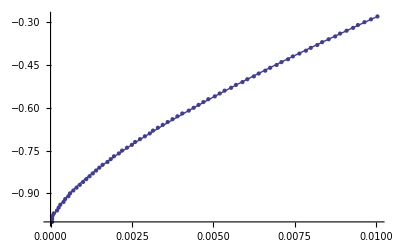

```mathematica
Show[ListPlot[stabline], Plot[fitstab, {x, 0, 0.01}]]
```

```mathematica
Export["k1k1chaos.pdf",k1k1chaos,"AllowRasterization"->True,ImageResolution->600]
```

k1k1chaos.pdf

```mathematica
k2k2chaos:=Show[ListDensityPlot[k2,PlotRange->All,InterpolationOrder->0,ColorFunctionScaling ->False,ColorFunction->(ColorData["SunsetColors"][(#/3.1+0.05)]&),PlotLegends->BarLegend[Automatic,LabelStyle->Directive[FontSize->12],LegendLabel->Placed["λ_L",Right]]],ListLinePlot[stabline,PlotStyle->{White,Dashed,Thickness[0.01]}],FrameLabel->{λ,Γ,"k_x=k_y=2"},BaseStyle->{FontSize->12}]
```

```mathematica
k2k1chaos:=Show[ListDensityPlot[k21,PlotRange->All,InterpolationOrder->0,ColorFunctionScaling ->False,ColorFunction->(ColorData["SunsetColors"][(#/3.1+0.05)]&),PlotLegends->BarLegend[Automatic,LabelStyle->Directive[FontSize->12],LegendLabel->Placed["λ_L",Right]]],ListLinePlot[stabline,PlotStyle->{White,Dashed,Thickness[0.01]}],FrameLabel->{λ,Γ,"k_x=2,k_y=1"},BaseStyle->{FontSize->12}]
```

```mathematica
Export["k2k2chaos2.pdf",k2k2chaos,"AllowRasterization"->True,ImageResolution->600]
```

k2k2chaos2.pdf

```mathematica
Export["k2k1chaos.pdf",k2k1chaos,"AllowRasterization"->True,ImageResolution->600]
```

k2k1chaos.pdf